# Osciladores Acoplados

#### Didáctica de la Física

Diego Sarceño
201900109

```mathematica
(* Constantes del sistema *)
k1=k3=6
k2=2
m1=2
m2=4
```

6

2

2

4

```mathematica
(* Solución numérica al sistema de ecuaciones acopladas *)
s=NDSolve[{x''[t]==(-(k1+k2))/m1*x[t]+k2/m1*y[t],y''[t]==k3/m2*x[t]-(k2+k3)/m2*y[t],x[0]==1,y[0]==2,x'[0]==0,y[0]==0},{x,y},{t,50}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

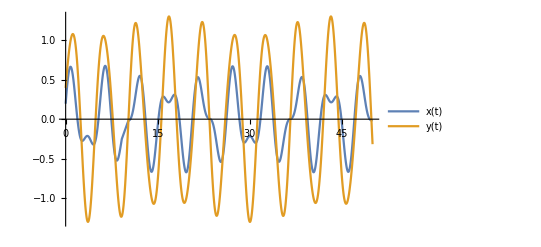

```mathematica
(* Gráfica en el tiempo de la posición de ambas masas *)
Plot[Evaluate[{x[t],y[t]}/.s],{t,0,50},PlotLegends->{"x(t)","y(t)"}]
```

## Desacoplamiento

```mathematica
MatrixForm[M={{2,-1},{-1,2}}] (* Operador *)
```

(2 | -1
-1 | 2)

```mathematica
sis=Eigensystem[M] (* Valores y vectores propios *)
```

{{3,1},{{-1,1},{1,1}}}

```mathematica
(* Valores *)
sis[[1]]
(* Vectores *)
sis[[2]]
```

{3,1}

{{-1,1},{1,1}}

```mathematica
Solve[{-a*w1+b*w2==0,a*w1+b*w2==0},{a,b}]
```

{{a→0,b→0}}

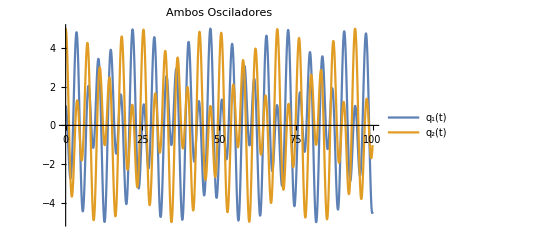

```mathematica
(* Grafico *)
Plot[{Cos[((√3+1)*x)/2]*Cos[((√3-1)*x)/2]+5*Sin[((√3+1)*x)/2]*Sin[((-√3+1)*x)/2],5*Cos[((√3+1)*x)/2]*Cos[((√3-1)*x)/2]+Sin[((√3+1)*x)/2]*Sin[((-√3+1)*x)/2]},{x,0,100},PlotLabel->"Ambos Osciladores",PlotLegends->{"q_1(t)","q_2(t)"}]
```

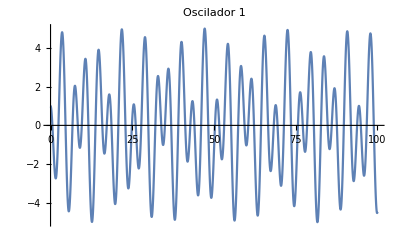

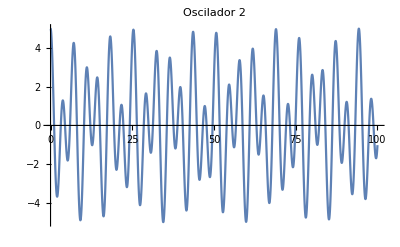

```mathematica
(* Separados *)
Plot[{Cos[((√3+1)*x)/2]*Cos[((√3-1)*x)/2]+5*Sin[((√3+1)*x)/2]*Sin[((-√3+1)*x)/2]},{x,0,100},PlotLabel->"Oscilador 1",PlotLegends->"q_1(t)"]
Plot[{5*Cos[((√3+1)*x)/2]*Cos[((√3-1)*x)/2]+Sin[((√3+1)*x)/2]*Sin[((-√3+1)*x)/2]},{x,0,100},PlotLabel->"Oscilador 2",PlotLegends->"q_2(t)"]
```